Université Pierre et Marie Curie |                                         | UE Transversale 1XM01Mathematica

__________________________________________________________________________

M 1 : Introduction à Mathematica
__________________________________________________________________________

## Exercices

Le fichier doit être renommé exactement comme ceci :
	M1VotrenomPrenom.nb
Cela permet à vos enseignants de s’y retrouver et de ne pas avoir à renommer tous les fichiers. Merci.
	Votrenom avec une seule majuscule
	Prenom avec une seule majuscule
	Pas de blanc, ni souligné, ni accent, ni symbole particulier
Ce fichier doit être déposé sur SAKAI à la fin de la séance, et/ou avant la fin de la semaine de la séance.

## I. Interface

### A. Mise en forme

#### 1. Les cellules et leur hiérarchie

Reproduire avec l’Interface de Mathematica la présentation suivante :

# Chapitre M 1

## Jinxin Wang 3404759

Vendredi 30 01 2015

## I. Mise en Forme Générale

### A: L’interface

### 1 sous-sous-section n°1

texte

texte : la cellule ci-dessous est une cellule d’”Input”

```mathematica
3+ 5
```

### 1 sous-sous-section n°2

texte

texte : la cellule ci-dessous est une autre cellule d’”Input”

### B: Le Noyau

### 1 sous-sous-section n°1

texte

texte : la cellule ci-dessous est encore une autre cellule d’”Input”

## II. Mise en Forme Spécifique

### A: Saisie

### 1. Avec la palette Texte (Writing Assistant)

Dans une cellulle “Texte” saisir les formules :

∑_(i=1)^10 i           ∑_(i=1)^n i             (1 | 2
3 | 4)

### 2. Avec la palette Input (Basic Math Assistant)

Dans une cellulle “Input” saisir les formules :

```mathematica
∑_(i=1)^10 i          ∑_(i=1)^n i          ({{1, 2}, {3, 4}})
```

### 3. Avec la palette et les raccourcis clavier

```mathematica
∑_(i=1)^10 i^2      ∑_(i=1)^n i^2        ({{α, β}, {γ, δ}})
```

### 4. Avec la palette et les raccourcis clavier

Saisir sous une forme plus “traditionnelle” ou moin “informatique” l’expression :

```mathematica
(x^5+4x^3+2)Exp[-(y^2)/2]/√pi
```

```mathematica
((x^5+ 4 x^3+2)e^(-y^2/2))/(√π)
```

## II. Un tour introductif

→ Expliquer ce qui se passe quand vous validez les cellules :

### A. Opérations de base (symboliques avec précision arbitraire)

```mathematica
Bonjour!
```

Bonjour!

Output revoie le input

#### 1. Élémentaire

Calculation algébrique

```mathematica
1+1
```

2

Calculation symbolique

```mathematica
4€+5€
```

9 €

Calculation géométrie

```mathematica
Cos[Pi]
```

-1

Calculation limitatif

```mathematica
Cos[x] /. x -> π
```

-1

Calculation symbolique

```mathematica
3x + 2 x
```

5 x

#### 2. Les quatre opérations :

```mathematica
31 5
315/14
3^100
```

155

45/2

515377520732011331036461129765621272702107522001

#### 3. Valeurs numériques approchées : N[]

```mathematica
N[315/14]
N[3^100]
N[3^100, 20]
```

22.5

5.15378×10^47

5.1537752073201133104×10^47

```mathematica
N[315/14]
N[3^100]
N[3^100, 20]
```

22.5

5.15378×10^47

5.1537752073201133104×10^47

#### 4. Quelques tests utiles pour comprendre

//Timing est une function qui revoie le time de la calculation
Le premier valeur revoyé est le time de la calculation
Le deuxième est nul parce que “;” est utilsé

```mathematica
3^100;//Timing
3^1000;//Timing
3^10000;//Timing
3^100000;//Timing
3^1000000;//Timing
3^10000000;//Timing
3^100000000;//Timing
3^1000000000;//Timing
```

{0.00001,Null}

{6.×10^-6,Null}

{0.00002,Null}

{0.00034,Null}

{0.00442,Null}

{0.0677,Null}

{0.86666,Null}

{12.00749,Null}

```mathematica
N[3^100000000];//Timing
N[3.^100000000]//Timing
```

{0.92528,Null}

{0.,2.964600951548×10^47712125}

#### 5. Exemples récapitulatifs

```mathematica
N [π]
```

3.14159

```mathematica
π //N
```

3.14159

```mathematica
N[π,30]
```

3.14159265358979323846264338328

```mathematica
N[π,2000]
```

3.1415926535897932384626433832795028841971693993751058209749445923078164062862089986280348253421170679821480865132823066470938446095505822317253594081284811174502841027019385211055596446229489549303819644288109756659334461284756482337867831652712019091456485669234603486104543266482133936072602491412737245870066063155881748815209209628292540917153643678925903600113305305488204665213841469519415116094330572703657595919530921861173819326117931051185480744623799627495673518857527248912279381830119491298336733624406566430860213949463952247371907021798609437027705392171762931767523846748184676694051320005681271452635608277857713427577896091736371787214684409012249534301465495853710507922796892589235420199561121290219608640344181598136297747713099605187072113499999983729780499510597317328160963185950244594553469083026425223082533446850352619311881710100031378387528865875332083814206171776691473035982534904287554687311595628638823537875937519577818577805321712268066130019278766111959092164201989380952572010654858632788659361533818279682303019520353018529689957736225994138912497217752834791315155748572424541506959508295331168617278558890750983817546374649393192550604009277016711390098488240128583616035637076601047101819429555961989467678374494482553797747268471040475346462080466842590694912933136770289891521047521620569660240580381501935112533824300355876402474964732639141992726042699227967823547816360093417216412199245863150302861829745557067498385054945885869269956909272107975093029553211653449872027559602364806654991198818347977535663698074265425278625518184175746728909777727938000816470600161452491921732172147723501414419735685481613611573525521334757418494684385233239073941433345477624168625189835694855620992192221842725502542568876717904946016534668049886272327917860857843838279679766814541009538837863609506800642251252051173929848960841284886269456042419652850222106611863067442786220391949450471237137869609563643719172874677646575739624138908658326459958133904780275901

### B. Opérations de base (numériques)

```mathematica
(10.2-3.1)*6.2/2.9
```

15.1793

```mathematica
(2+3I)*(4-5I)
```

23+2 ⅈ

### C. Nombres et Fonctions élémentaires

#### 1. Quelques constantes mathématiques

→ Saisir dans une cellule input (sans faire de copier coller !!!)

- le nombre π

```mathematica
π == Pi
```

- le nombre e

```mathematica
ⅇ == E
```

- le nombre imaginaire i

```mathematica
ⅈ == I
```

- l'infini ∞ :

```mathematica
∞ == Infinity
```

#### 2. Quelques fonctions mathématiques

Mathematica dispose de nombreuses fonctions prédéfinies dont le nom suit la règle Nom[] :

→ Comment écrit-on dans une cellule input (sans faire de copier coller non plus !!!) les fonctions suivantes :

- racine carrée : √x

```mathematica
Sqrt[x]
```

- exponentielle : e^x

```mathematica
Exp[x]
```

- logarithme népérien : ln(x)

```mathematica
Log[x]
```

- logarithme en base b : log_b(x)  (le plus souvent, b=10)

```mathematica
Log[b,x]
```

- fonctions trigonométriques :

```mathematica
Sin[x]
Cos[x]
Tan[x]
Cot[x]
```

- fonctions trigonométriques inverses :

```mathematica
ArcSin[x]
ArcCos[x]
ArcTan[x]
ArcCot[x]
```

- valeur absolue : |x|

```mathematica
Abs[x]
```

- factorielle : n !

```mathematica
Factorial[n]
```

→ Sélectionnez la fonction Cos[] et tapez sur F1 (sous PC) ou ⌘ F (sous Mac) pour afficher la page d'aide de cette fonction.

→ Explorez d’autres fonctions avec la rubrique SEE ALSO “ref/ArcCos”

```mathematica
http://reference.wolfram.com/language/ref/ArcCos.html?q=ArcCos
```

→ Revenez à la page d’aide précédente, et explorez TUTORIALS “tutorial/SomeMathematicalFunctions” qui donne une petite liste des fonctions élémentaires

→ Revenez à la page d’aide précédente, et explorez MORE ABOUT  “guide/SomeMathematicalFunctions” qui donne la liste des fonctions élémentaires

```mathematica
"guide/SomeMathematicalFunctions" n'est pas trouvé, mais il existe  "\"""guide""/""MathematicalFunctions""\""
```

### D. Fonctions

#### 1. Programmation procédurale et fonctionnelle

#### 2. Mode d’utilisation d’une fonction

En dehors de la notation fonctionnel standard Nom[argument1, argument2, ...], il y a trois façons d’utiliser ou de noter les fonctions :
		Prefix 
		Infix
		Postfix

```mathematica
Plus[2,3] == 2~Plus~3 == (2+3)
```

```mathematica
Sqrt[3] == 3 // Sqrt == √3
```

→ Quelles sont les notations Infix pour l’addition “+“ , la multiplication “*”, la soustraction “-”, la division “/”, la puissance, →,   /. .... ?

{}

```mathematica
Infix : Plus,Subtract, Times, Divide, Power, Rule,ReplaceAll,etc.
```

#### 3. Composition de fonctions

→ Saisir dans une cellule “Input”, et constater que la hiérarchie d’indentation est automatiquement respectée à chaque retour à la ligne :

Plot[
 Cos[x],
 {x, -2 π, 2 π}
 ]

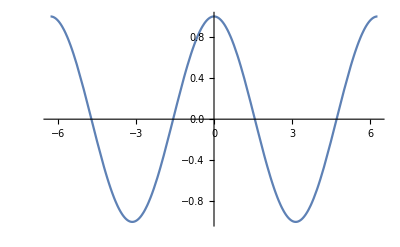

```mathematica
Plot[
Cos[x],
{x,-2π,2π}
]
```

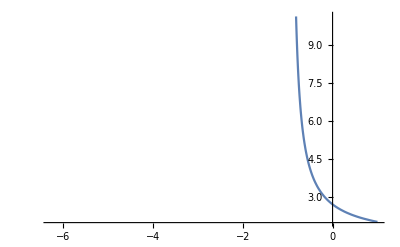

```mathematica
Plot[Exp[Cos[ArcTan[√x]]],{x,-2π,1}]
```

Manipulate[
 Plot[
  Cos[a x + b],
  {x, -2 π, 2 π}
  ],
 {a, 1, 10},
 {b, 0, 2 π}
 ]

```mathematica
Manipulate[
Plot[
Cos[ax+b],
{x,-2π,2π}
],
{a,1,10},
{b,0,2π}
]
```

→ Puis jouez avec les curseurs !

#### 4. Arguments et Options des Fonctions : tracer de courbes

Les fonctions ont généralement des arguments obligatoires, et un certain nombre d’Options que l’on peut ou non rajouter pour préciser la fonction. Étudions la fonction très utile Plot[] au travers des exemples suivants :

→ Tracer, ⅇ^-x Sin[2 π x]

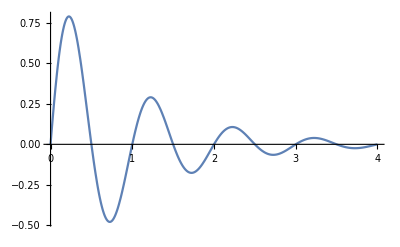

```mathematica
Plot[ⅇ^-x Sin[2π x],{x,0,4}]
```

→ Idem en rajoutant en option AxesLabel→{“Time”,”Ampl.”}, pour spécifier les axes.
Elle consiste à remplir avec les contenus donnés dans la liste {“Time”,”Ampl.”} la variable AxesLabel :

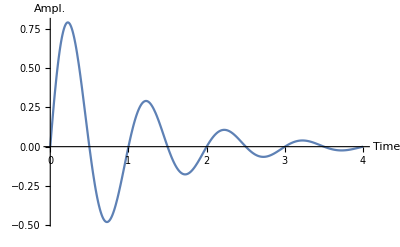

```mathematica
Plot[ⅇ^-x Sin[2π x],{x,0,4},AxesLabel->{"Time","Ampl."}]
```

→ Tracé de plusieurs fonctions sur le même graphe au moyen d’une liste de fonctions :
		 { ⅇ^-x Sin[2 π x],Exp[-x],-Exp[-x] }

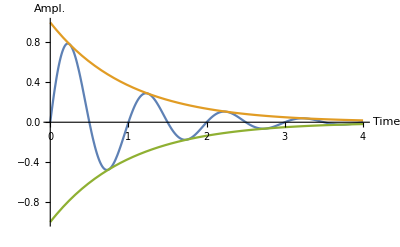

```mathematica
Plot[{ⅇ^-x Sin[2π x],Exp[-x],-Exp[-x]},{x,0,4},AxesLabel->{"Time","Ampl."}]
```

→ Mettez des couleurs, et des couleurs

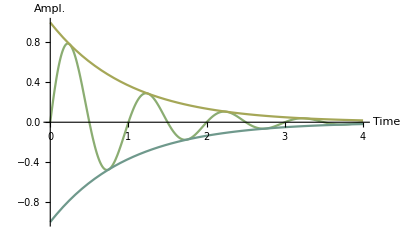

```mathematica
Plot[{ⅇ^-x Sin[2π x],Exp[-x],-Exp[-x]},{x,0,4},AxesLabel->{"Time","Ampl."},ColorFunction->"Rainbow"]
```

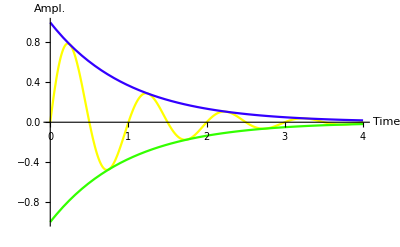

```mathematica
Plot[{ⅇ^-x Sin[2π x],Exp[-x],-Exp[-x]},{x,0,4},AxesLabel->{"Time","Ampl."},PlotStyle-> {RGBColor[1,1,0],Hue[0.7],Hue[0.3]}]
```

#### 5. Définition de nouvelle fonction par l’utilisateur

→ Définissez la fonction f(x) = (a x^4)/(b+x^4) , pour cela écrire, puis valider la fonction pour qu’elle soit connue du noyau :

```mathematica
f[x_]:=(a x^4)/(b+x^4)
```

→ Vérifiez que f est correctement définie :

```mathematica
f[3]
```

(81 a)/(81+b)

```mathematica
?f
```

Global`f

f[x_]:=(a x^4)/(b+x^4)

→ Vérifiez que cette fonction est utilisable avec n’importe quel argument, valeur ou expression :

```mathematica
f[α]
f[7]
f[a+b]
```

(a α^4)/(b+α^4)

(2401 a)/(2401+b)

(a (a+b)^4)/(b+(a+b)^4)

```mathematica
g[x_,y_]:=(a x)/(b+x)+(b y^4)/(b+y^4)
```

```mathematica
?g
```

Global`g

g[x_,y_]:=(a x)/(b+x)+(b y^4)/(b+y^4)

```mathematica
g[α+√2 β+0.3,α/β]
```

(b α^4)/((b+α^4/β^4) β^4)+(a (0.3+α+√2 β))/(0.3+b+α+√2 β)

#### 6. Éléments d’étude de fonction

→ Calcul de la première dérivée de f  :

```mathematica
D[f[α],α]
```

-(4 a α^7)/((b+α^4)^2)+(4 a α^3)/(b+α^4)

→ Quelle est la notation fonctionnelle de la dérivation ‘ ?
→ On peut facilement calculer la cinquième dérivée.

```mathematica
f'[x]
f''[x]
f'''[x]
f''''[x]
f'''''[x]
```

-(4 a x^7)/((b+x^4)^2)+(4 a x^3)/(b+x^4)

(32 a x^10)/((b+x^4)^3)-(44 a x^6)/((b+x^4)^2)+(12 a x^2)/(b+x^4)

-(384 a x^13)/((b+x^4)^4)+(672 a x^9)/((b+x^4)^3)-(312 a x^5)/((b+x^4)^2)+(24 a x)/(b+x^4)

(6144 a x^16)/((b+x^4)^5)-(13056 a x^12)/((b+x^4)^4)+(8544 a x^8)/((b+x^4)^3)-(1656 a x^4)/((b+x^4)^2)+(24 a)/(b+x^4)

-(122880 a x^19)/((b+x^4)^6)+(307200 a x^15)/((b+x^4)^5)-(259200 a x^11)/((b+x^4)^4)+(81600 a x^7)/((b+x^4)^3)-(6720 a x^3)/((b+x^4)^2)

→ Calcul des asymptotes :

```mathematica
Limit[f[x],x->0.5]
Limit[f[x],x->∞]
Limit[f[x],x->-b]
```

(0.0625 a)/(0.0625+b)

a

(a b^3)/(1+b^3)

→ Calcul de valeurs particulières :

```mathematica
Limit[f'[x],x->0]
```

0

→ Calcul de valeurs particulières par résolution d’équations :
recherchez la valeur de s pour laquelle f[s] est la moitié de la valeur maximale atteignable

```mathematica
Solve[f[s]==a/2,s]
```

{{s→-b^(1/4)},{s→-ⅈ b^(1/4)},{s→ⅈ b^(1/4)},{s→b^(1/4)}}

→ Tracé de courbes :

Plot[
 {f[x], 10} /. {a -> 10.0, b -> 5.0},
 {x, -5, 5}, 
 PlotRange -> {-5, 10}
 ]

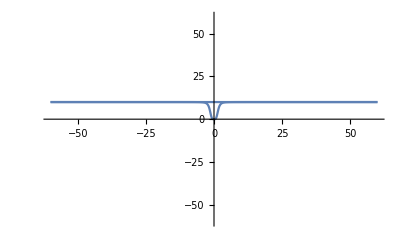

```mathematica
Plot[
{f[x], 10}/.{a->10.0,b->5.0},
{x,-60,60},
PlotRange->{-60,60}
]
```

→ Que remarque-t-on ?

En pratique, cette fonction n’est intéressante que pour des valeurs réelles. On résume les résultats dans le graphique :

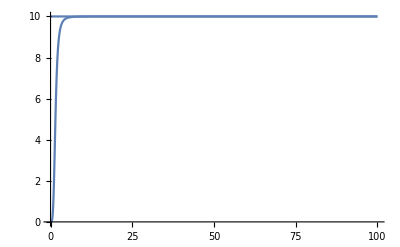

```mathematica
Plot[
{f[x], 10}/.{a->10.0,b->5.0},
{x,0,100},
PlotRange->All
]
```

→ Montrer que f conserve sa définition symbolique :

```mathematica
f[s]
```

(a s^4)/(b+s^4)

### E. Graphiques 2D, 3D, sons et animations

#### 1. Représentation graphique

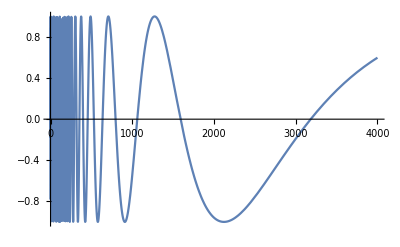

```mathematica
Plot[Sin[10000/t],{t,0,4000}]
```

Mais on arrive toujours à mettre le système en difficulté (Expliquer pourquoi ?):

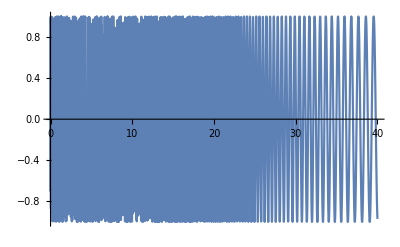

```mathematica
Plot[Sin[10000/t],{t,0,40}]
```

#### 2. Représentation sonore

On peut d’ailleurs l’écouter, pour ce convaincre de la pathologie de la fonction en ce point. On remarquera que les singularités du type 1/0 ne sont pas un obstacle, ce qui est très appréciable.

```mathematica
Play[Sin[10000/t],{t,-2,-0.001}]
```

-Graphics-

#### 2. Tracé de fonction en 3 dimensions - Animation 3D

Tracé en 3D d’une fonction simple. On trouve ce type de courbe pour décrire la surface d’un cristal.

```mathematica
Plot3D[Sin[x] Sin[y],{x,-5,5},{y,-5,5},PlotPoints->30]
```

-Graphics3D-

```mathematica
Manipulate[
Plot3D[Sin[a x+b] Sin[y],{x,-5,5},{y,-5,5},PlotPoints->30],
{a,1,5},
{b,0,π}
]
```